```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: PacletObject[…].

It can now be loaded using the command <<IGraphM`

```mathematica
<<IGraphM`
```

IGDocumentation::shdw: Symbol IGDocumentation appears in multiple contexts {IGraphM`,Global`}; definitions in context IGraphM` may shadow or be shadowed by other definitions.

IGraph/M 0.5.1 (October 12, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
IGDocumentation[]
```

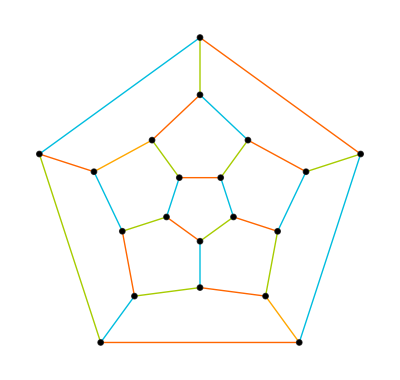

```mathematica
Graph[GraphData["DodecahedralGraph"],EdgeStyle->Directive[Thick,Opacity[1]],VertexStyle->Black]//IGEdgeMap[ColorData[109],EdgeStyle->IGEdgeColoring]
```

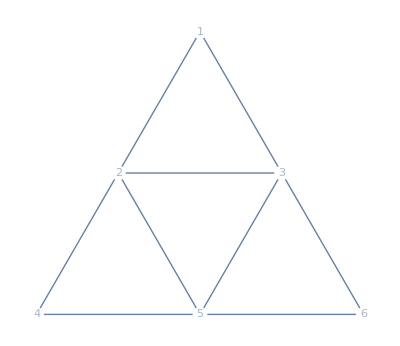

```mathematica
g=IGTriangularLattice[3,VertexShapeFunction->"Name"]
```

{{1,2,3},{1,3,6,5,4,2},{2,4,5},{2,5,3},{3,5,6}}

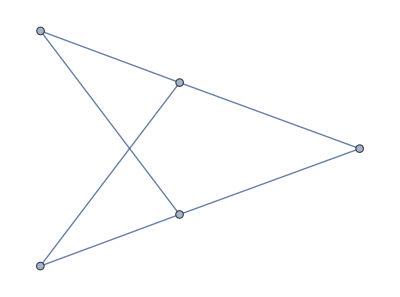

```mathematica
IGFaces[g]
IGDualGraph[g]
```

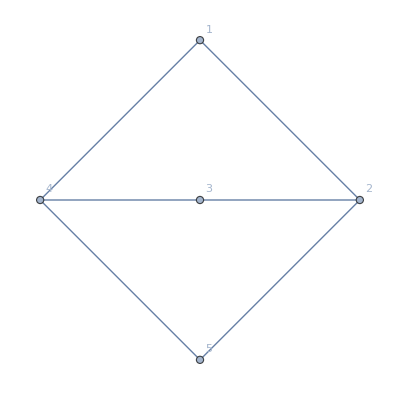

```mathematica
PlanarGraph[IGDualGraph[g,VertexLabels->"Name"]]
```

```mathematica
adjv7f81=Normal[AdjacencyMatrix[{1<->2,2<->3,3<->4,1<->4,5<->6,6<->7,5<->7,1<->5,1<->7,4<->7,3<->6,3<->7,2<->6}]]
```

{{0,1,0,1,1,0,1},{1,0,1,0,0,1,0},{0,1,0,1,0,1,1},{1,0,1,0,0,0,1},{1,0,0,0,0,1,1},{0,1,1,0,1,0,1},{1,0,1,1,1,1,0}}

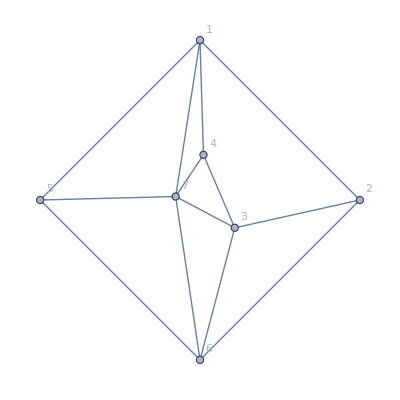

```mathematica
adjv7f81g=PlanarGraph[AdjacencyGraph[adjv7f81,VertexLabels->"Name"]]
```

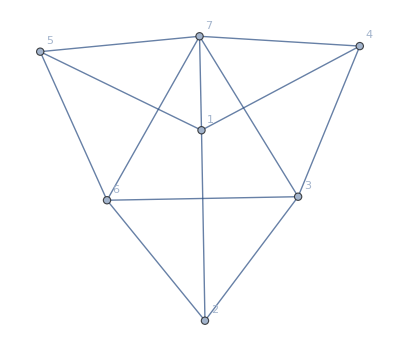

```mathematica
AdjacencyGraph[adjv7f81,VertexLabels->"Name"]
```

```mathematica
IGFaces[adjv7f81g]
```

{{1,2,3,4},{1,4,7},{1,7,5},{1,5,6,2},{2,6,3},{3,6,7},{3,7,4},{5,7,6}}

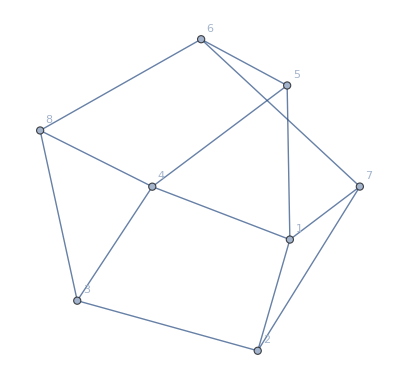

```mathematica
IGDualGraph[adjv7f81g,VertexLabels->"Name"]
```

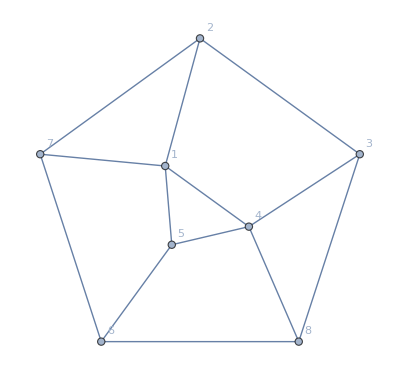

```mathematica
adjv7f81dg=PlanarGraph[IGDualGraph[adjv7f81g,VertexLabels->"Name"]]
```

```mathematica
IGFaces[adjv7f81dg]
```

{{1,4,5},{1,5,6,7},{1,7,2},{1,2,3,4},{2,7,6,8,3},{3,8,4},{4,8,6,5}}

```mathematica
adjv7f81d=Normal[AdjacencyMatrix[adjv7f81dg]]
```

{{0,1,0,1,1,0,1,0},{1,0,1,0,0,0,1,0},{0,1,0,1,0,0,0,1},{1,0,1,0,1,0,0,1},{1,0,0,1,0,1,0,0},{0,0,0,0,1,0,1,1},{1,1,0,0,0,1,0,0},{0,0,1,1,0,1,0,0}}

```mathematica
Table[If[i==j,1,If[adjv7f81[[i,j]]==1,-1,If[i>j,Subscript[b, j,i],Subscript[b, i,j],]]],{i,1,VertexCount[adjv7f81g]},{j,1,VertexCount[adjv7f81g]}]//MatrixForm
```

(1 | -1 | b_(1,3) | -1 | -1 | b_(1,6) | -1
-1 | 1 | -1 | b_(2,4) | b_(2,5) | -1 | b_(2,7)
b_(1,3) | -1 | 1 | -1 | b_(3,5) | -1 | -1
-1 | b_(2,4) | -1 | 1 | b_(4,5) | b_(4,6) | -1
-1 | b_(2,5) | b_(3,5) | b_(4,5) | 1 | -1 | -1
b_(1,6) | -1 | -1 | b_(4,6) | -1 | 1 | -1
-1 | b_(2,7) | -1 | -1 | -1 | -1 | 1)

```mathematica
Table[If[i==j,1,If[adjv7f81d[[i,j]]==1,-1,If[i>j,Subscript[b, j+VertexCount[adjv7f81g],i+VertexCount[adjv7f81g]],Subscript[b, i+VertexCount[adjv7f81g],j+VertexCount[adjv7f81g]],]]],{i,1,VertexCount[adjv7f81dg]},{j,1,VertexCount[adjv7f81dg]}]//MatrixForm
```

(1 | -1 | b_(8,10) | -1 | -1 | b_(8,13) | -1 | b_(8,15)
-1 | 1 | -1 | b_(9,11) | b_(9,12) | b_(9,13) | -1 | b_(9,15)
b_(8,10) | -1 | 1 | -1 | b_(10,12) | b_(10,13) | b_(10,14) | -1
-1 | b_(9,11) | -1 | 1 | -1 | b_(11,13) | b_(11,14) | -1
-1 | b_(9,12) | b_(10,12) | -1 | 1 | -1 | b_(12,14) | b_(12,15)
b_(8,13) | b_(9,13) | b_(10,13) | b_(11,13) | -1 | 1 | -1 | -1
-1 | -1 | b_(10,14) | b_(11,14) | b_(12,14) | -1 | 1 | b_(14,15)
b_(8,15) | b_(9,15) | -1 | -1 | b_(12,15) | -1 | b_(14,15) | 1)

```mathematica
Clear[i]
```

```mathematica
Table[If[MemberQ[IGFaces[adjv7f81g][[j]],i],0,Subscript[b, j+VertexCount[adjv7f81g],i]],{i,VertexCount[adjv7f81g]},{j,VertexCount[adjv7f81dg]}]//MatrixForm
```

(0 | 0 | 0 | 0 | b_(12,1) | b_(13,1) | b_(14,1) | b_(15,1)
0 | b_(9,2) | b_(10,2) | 0 | 0 | b_(13,2) | b_(14,2) | b_(15,2)
0 | b_(9,3) | b_(10,3) | b_(11,3) | 0 | 0 | 0 | b_(15,3)
0 | 0 | b_(10,4) | b_(11,4) | b_(12,4) | b_(13,4) | 0 | b_(15,4)
b_(8,5) | b_(9,5) | 0 | 0 | b_(12,5) | b_(13,5) | b_(14,5) | 0
b_(8,6) | b_(9,6) | b_(10,6) | 0 | 0 | 0 | b_(14,6) | 0
b_(8,7) | 0 | 0 | b_(11,7) | b_(12,7) | 0 | 0 | 0)

```mathematica
Table[If[MemberQ[IGFaces[adjv7f81g][[j]],i],0,If[i>j,Subscript[b, i+VertexCount[adjv7f81g],j],Subscript[b, i+VertexCount[adjv7f81g],j]]],{i,1,VertexCount[adjv7f81g]},{j,1,VertexCount[adjv7f81dg]}]//MatrixForm
```

(0 | 0 | 0 | 0 | b_(8,5) | b_(8,6) | b_(8,7) | b_(8,8)
0 | b_(9,2) | b_(9,3) | 0 | 0 | b_(9,6) | b_(9,7) | b_(9,8)
0 | b_(10,2) | b_(10,3) | b_(10,4) | 0 | 0 | 0 | b_(10,8)
0 | 0 | b_(11,3) | b_(11,4) | b_(11,5) | b_(11,6) | 0 | b_(11,8)
b_(12,1) | b_(12,2) | 0 | 0 | b_(12,5) | b_(12,6) | b_(12,7) | 0
b_(13,1) | b_(13,2) | b_(13,3) | 0 | 0 | 0 | b_(13,7) | 0
b_(14,1) | 0 | 0 | b_(14,4) | b_(14,5) | 0 | 0 | 0)

```mathematica
ArrayFlatten[{{Table[If[i==j,1,If[adjv7f81[[i,j]]==1,-1,If[i>j,Subscript[b, j,i],Subscript[b, i,j]]]],{i,1,VertexCount[adjv7f81g]},{j,1,VertexCount[adjv7f81g]}],Table[If[MemberQ[IGFaces[adjv7f81g][[j]],i],0,Subscript[b, j+VertexCount[adjv7f81g],i]],{i,VertexCount[adjv7f81g]},{j,VertexCount[adjv7f81dg]}]},{Transpose[Table[If[MemberQ[IGFaces[adjv7f81g][[j]],i],0,Subscript[b, j+VertexCount[adjv7f81g],i]],{i,VertexCount[adjv7f81g]},{j,VertexCount[adjv7f81dg]}]],Table[If[i==j,1,If[adjv7f81d[[i,j]]==1,-1,If[i>j,Subscript[b, j+VertexCount[adjv7f81g],i+VertexCount[adjv7f81g]],Subscript[b, i+VertexCount[adjv7f81g],j+VertexCount[adjv7f81g]]]]],{i,1,VertexCount[adjv7f81dg]},{j,1,VertexCount[adjv7f81dg]}]}}]//MatrixForm
```

(1 | -1 | b_(1,3) | -1 | -1 | b_(1,6) | -1 | 0 | 0 | 0 | 0 | b_(12,1) | b_(13,1) | b_(14,1) | b_(15,1)
-1 | 1 | -1 | b_(2,4) | b_(2,5) | -1 | b_(2,7) | 0 | b_(9,2) | b_(10,2) | 0 | 0 | b_(13,2) | b_(14,2) | b_(15,2)
b_(1,3) | -1 | 1 | -1 | b_(3,5) | -1 | -1 | 0 | b_(9,3) | b_(10,3) | b_(11,3) | 0 | 0 | 0 | b_(15,3)
-1 | b_(2,4) | -1 | 1 | b_(4,5) | b_(4,6) | -1 | 0 | 0 | b_(10,4) | b_(11,4) | b_(12,4) | b_(13,4) | 0 | b_(15,4)
-1 | b_(2,5) | b_(3,5) | b_(4,5) | 1 | -1 | -1 | b_(8,5) | b_(9,5) | 0 | 0 | b_(12,5) | b_(13,5) | b_(14,5) | 0
b_(1,6) | -1 | -1 | b_(4,6) | -1 | 1 | -1 | b_(8,6) | b_(9,6) | b_(10,6) | 0 | 0 | 0 | b_(14,6) | 0
-1 | b_(2,7) | -1 | -1 | -1 | -1 | 1 | b_(8,7) | 0 | 0 | b_(11,7) | b_(12,7) | 0 | 0 | 0
0 | 0 | 0 | 0 | b_(8,5) | b_(8,6) | b_(8,7) | 1 | -1 | b_(8,10) | -1 | -1 | b_(8,13) | -1 | b_(8,15)
0 | b_(9,2) | b_(9,3) | 0 | b_(9,5) | b_(9,6) | 0 | -1 | 1 | -1 | b_(9,11) | b_(9,12) | b_(9,13) | -1 | b_(9,15)
0 | b_(10,2) | b_(10,3) | b_(10,4) | 0 | b_(10,6) | 0 | b_(8,10) | -1 | 1 | -1 | b_(10,12) | b_(10,13) | b_(10,14) | -1
0 | 0 | b_(11,3) | b_(11,4) | 0 | 0 | b_(11,7) | -1 | b_(9,11) | -1 | 1 | -1 | b_(11,13) | b_(11,14) | -1
b_(12,1) | 0 | 0 | b_(12,4) | b_(12,5) | 0 | b_(12,7) | -1 | b_(9,12) | b_(10,12) | -1 | 1 | -1 | b_(12,14) | b_(12,15)
b_(13,1) | b_(13,2) | 0 | b_(13,4) | b_(13,5) | 0 | 0 | b_(8,13) | b_(9,13) | b_(10,13) | b_(11,13) | -1 | 1 | -1 | -1
b_(14,1) | b_(14,2) | 0 | 0 | b_(14,5) | b_(14,6) | 0 | -1 | -1 | b_(10,14) | b_(11,14) | b_(12,14) | -1 | 1 | b_(14,15)
b_(15,1) | b_(15,2) | b_(15,3) | b_(15,4) | 0 | 0 | 0 | b_(8,15) | b_(9,15) | -1 | -1 | b_(12,15) | -1 | b_(14,15) | 1)

```mathematica
Clear[adjmat]
```

```mathematica
pgraph[adjmat_]:=PlanarGraph[AdjacencyGraph[adjmat,VertexLabels->"Name"]]
```

```mathematica
dgraph[adjmat_]:=PlanarGraph[IGDualGraph[pgraph[adjmat],VertexLabels->"Name"]]
```

```mathematica
dadjmat[adjmat_]:=Normal[AdjacencyMatrix[dgraph[adjmat]]]
```

```mathematica
exGmat[adjmat_,adjmatg_,adjmatd_,adjmatdg_]:=ArrayFlatten[{{Table[If[i==j,1,If[adjmat[[i,j]]==1,-1,If[i>j,Subscript[b, j,i],Subscript[b, i,j]]]],{i,1,VertexCount[adjmatg]},{j,1,VertexCount[adjmatg]}],Table[If[MemberQ[IGFaces[adjmatg][[j]],i],0,Subscript[b, j+VertexCount[adjmatg],i]],{i,VertexCount[adjmatg]},{j,VertexCount[adjmatdg]}]},{Transpose[Table[If[MemberQ[IGFaces[adjmatg][[j]],i],0,Subscript[b, j+VertexCount[adjmatg],i]],{i,VertexCount[adjmatg]},{j,VertexCount[adjmatdg]}]],Table[If[i==j,1,If[adjmatd[[i,j]]==1,-1,If[i>j,Subscript[b, j+VertexCount[adjmatg],i+VertexCount[adjmatg]],Subscript[b, i+VertexCount[adjmatg],j+VertexCount[adjmatg]]]]],{i,1,VertexCount[adjmatdg]},{j,1,VertexCount[adjmatdg]}]}}]
```

```mathematica
testshape=Normal[AdjacencyMatrix[{1<->2,1<->3,1<->4,1<->6,2<->3,2<->4,2<->5,3<->5,3<->6,4<->5,4<->6,5<->6}]]
```

{{0,1,1,1,1,0},{1,0,1,1,0,1},{1,1,0,0,1,1},{1,1,0,0,1,1},{1,0,1,1,0,1},{0,1,1,1,1,0}}

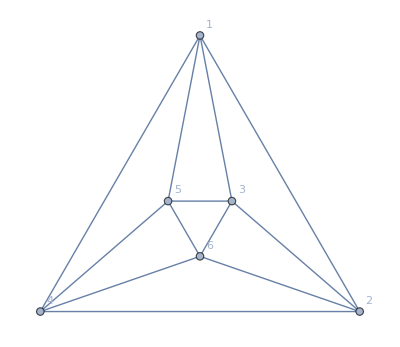

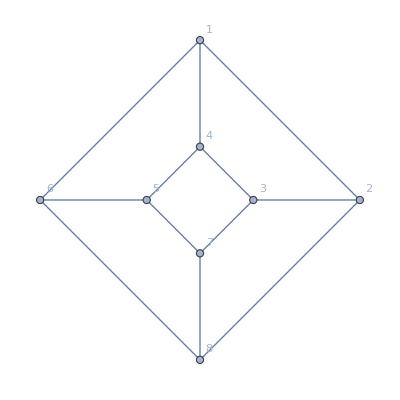

{{0,1,0,1,0,1,0,0},{1,0,1,0,0,0,0,1},{0,1,0,1,0,0,1,0},{1,0,1,0,1,0,0,0},{0,0,0,1,0,1,1,0},{1,0,0,0,1,0,0,1},{0,0,1,0,1,0,0,1},{0,1,0,0,0,1,1,0}}

```mathematica
pgraph[testshape]
dgraph[testshape]
dadjmat[testshape]
```

```mathematica
exocta=exGmat[testshape,pgraph[testshape],dadjmat[testshape],dgraph[testshape]]
```

{{1,-1,-1,-1,-1,b_(1,6),0,0,0,0,b_(11,1),b_(12,1),b_(13,1),b_(14,1)},{-1,1,-1,-1,b_(2,5),-1,0,b_(8,2),b_(9,2),0,0,0,b_(13,2),b_(14,2)},{-1,-1,1,b_(3,4),-1,-1,b_(7,3),b_(8,3),0,0,0,b_(12,3),0,b_(14,3)},{-1,-1,b_(3,4),1,-1,-1,0,0,b_(9,4),b_(10,4),b_(11,4),0,b_(13,4),0},{-1,b_(2,5),-1,-1,1,-1,b_(7,5),0,0,b_(10,5),b_(11,5),b_(12,5),0,0},{b_(1,6),-1,-1,-1,-1,1,b_(7,6),b_(8,6),b_(9,6),b_(10,6),0,0,0,0},{0,0,b_(7,3),0,b_(7,5),b_(7,6),1,-1,b_(7,9),-1,b_(7,11),-1,b_(7,13),b_(7,14)},{0,b_(8,2),b_(8,3),0,0,b_(8,6),-1,1,-1,b_(8,10),b_(8,11),b_(8,12),b_(8,13),-1},{0,b_(9,2),0,b_(9,4),0,b_(9,6),b_(7,9),-1,1,-1,b_(9,11),b_(9,12),-1,b_(9,14)},{0,0,0,b_(10,4),b_(10,5),b_(10,6),-1,b_(8,10),-1,1,-1,b_(10,12),b_(10,13),b_(10,14)},{b_(11,1),0,0,b_(11,4),b_(11,5),0,b_(7,11),b_(8,11),b_(9,11),-1,1,-1,-1,b_(11,14)},{b_(12,1),0,b_(12,3),0,b_(12,5),0,-1,b_(8,12),b_(9,12),b_(10,12),-1,1,b_(12,13),-1},{b_(13,1),b_(13,2),0,b_(13,4),0,0,b_(7,13),b_(8,13),-1,b_(10,13),-1,b_(12,13),1,-1},{b_(14,1),b_(14,2),b_(14,3),0,0,0,b_(7,14),-1,b_(9,14),b_(10,14),b_(11,14),-1,-1,1}}

```mathematica
Solve[Minors[exocta,5]==0,DeleteDuplicates[Cases[exocta,Subscript[b, _,_],2]]]
```

$Aborted

```mathematica
DeleteDuplicates[Cases[exocta,Subscript[b, _,_],2]]
```

{b_(1,6),b_(11,1),b_(12,1),b_(13,1),b_(14,1),b_(2,5),b_(8,2),b_(9,2),b_(13,2),b_(14,2),b_(3,4),b_(7,3),b_(8,3),b_(12,3),b_(14,3),b_(9,4),b_(10,4),b_(11,4),b_(13,4),b_(7,5),b_(10,5),b_(11,5),b_(12,5),b_(7,6),b_(8,6),b_(9,6),b_(10,6),b_(7,9),b_(7,11),b_(7,13),b_(7,14),b_(8,10),b_(8,11),b_(8,12),b_(8,13),b_(9,11),b_(9,12),b_(9,14),b_(10,12),b_(10,13),b_(10,14),b_(11,14),b_(12,13)}